# Period Doubling

We have seen how periodic orbits double and become chaotic.  We have seen how this behavior is universal. The key to understanding this was to look at and understand 1D maps g:[0,1]→[0,1].  We saw that all smooth single humped maps g had the same universal doubling behavior.  We ported this to the “peak” return map for the Rosseler system and found a whole bunch of stable periodic orbits.  We found enough stable periodic orbits that it looked as though they filled up the whole of the Rosseler attractor! This is the generic way that an ODE goes chaotic as you increase the non-linearity.

In words, it is common for a stable periodic orbit of a parameterized ODE y'=f_μ(y) with period T_u to transform to a stable periodic orbit of period 2 T_μ at a given value of the parameter μ^*.  It is common for this to happen repeatedly and this “frequency-doubling cascade” route to chaos is generic.

# Bifurcations

Interesting things can happen long before ODEs go chaotic.  The key is to think about how equilibrium points can change with the parameters. Changes in the nature of the equilibrium points are called bifurcations.

### Rosseler System

Lets look at the equilibrium points for the Rosseler system.

```mathematica
StdParams={0.2,0.2,5.7};
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z,x + a y, b+z(x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1+y,x,0},{z,0,-c+x}}
sub=Simplify[Solve[f[{a,b,c}][{x,y,z}]=={0,0,0},{x,y,z}]]
```

{{x→1/2 (c-√(-4 a b+c^2)),y→(-c+√(-4 a b+c^2))/(2 a),z→(c-√(-4 a b+c^2))/(2 a)},{x→1/2 (c+√(-4 a b+c^2)),y→-(c+√(-4 a b+c^2))/(2 a),z→(c+√(-4 a b+c^2))/(2 a)}}

```mathematica
Map[MatrixForm,Simplify[df[{a,b,c}][{x,y,z}]/.sub]]
```

{(0 | -1 | -1
1+(-c+√(-4 a b+c^2))/(2 a) | 1/2 (c-√(-4 a b+c^2)) | 0
(c-√(-4 a b+c^2))/(2 a) | 0 | 1/2 (-c-√(-4 a b+c^2))),(0 | -1 | -1
1-(c+√(-4 a b+c^2))/(2 a) | 1/2 (c+√(-4 a b+c^2)) | 0
(c+√(-4 a b+c^2))/(2 a) | 0 | 1/2 (-c+√(-4 a b+c^2)))}

It is standard to only change one parameter at a time which gives us curves for the eigenvalues in the complex plane.  Just a reminder that complex equilibrium points do not count and that the eigenvalues describe the behavior near the equilibrium point.  All of this can (and does) changes as you change the parameters in the ODE.

```mathematica
EqPtsRos[{a_,b_,c_}]:= {
{1/2 (c-√(-4 a b+c^2)),(-c+√(-4 a b+c^2))/(2 a),(c-√(-4 a b+c^2))/(2 a)},{1/2 (c+√(-4 a b+c^2)),-(c+√(-4 a b+c^2))/(2 a),(c+√(-4 a b+c^2))/(2 a)}}
EqEvalsRos[{a_,b_,c_}]:= Map[Eigenvalues, {
{{0,-1,-1},{1+(-c+√(-4 a b+c^2))/(2 a),1/2 (c-√(-4 a b+c^2)),0},{(c-√(-4 a b+c^2))/(2 a),0,1/2 (-c-√(-4 a b+c^2))}},{{0,-1,-1},{1-(c+√(-4 a b+c^2))/(2 a),1/2 (c+√(-4 a b+c^2)),0},{(c+√(-4 a b+c^2))/(2 a),0,1/2 (-c+√(-4 a b+c^2))}}
}]
```

```mathematica
cs=Range[0,5.7,0.1];
TabView[{
"1"->TabView[{
"EqPts"->TableForm[Chop[Table[EqPtsRos[{0.2,0.2,c}]⟦1⟧,{c,cs}]],TableHeadings->{cs,Automatic}],
"λs"->TableForm[Chop[Table[EqEvalsRos[{0.2,0.2,c}]⟦1⟧,{c,cs}]],TableHeadings->{cs,Automatic}]
},2],
"2"->TabView[{
"EqPts"->TableForm[Chop[Table[EqPtsRos[{0.2,0.2,c}]⟦2⟧,{c,cs}]],TableHeadings->{cs,Automatic}],
"λs"->TableForm[Chop[Table[EqEvalsRos[{0.2,0.2,c}]⟦2⟧,{c,cs}]],TableHeadings->{cs,Automatic}]
},2]
}]
```

12

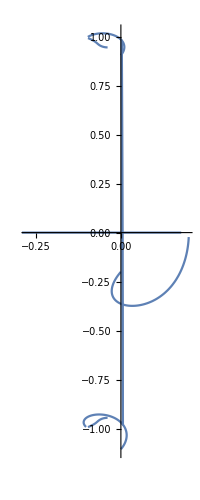

```mathematica
ParametricPlot[
ReIm[EqEvalsRos[{0.2,0.2,c}]]⟦1⟧,{c,0, 1}]
```

### VdP System

Lets look at the equilibrium points for the simpler VDP system.

```mathematica
f[μ_][{x_,y_}]:= {μ (1-y^2)x-y,x}
df[μ_][{x_,y_}]:={{(1-y^2) μ,-1-2 x y μ},{1,0}}
sub=Simplify[Solve[f[μ][{x,y}]=={0,0},{x,y}]]
```

{{x→0,y→0}}

```mathematica
Map[MatrixForm,A=Simplify[df[μ][{x,y}]/.sub]]
```

{(μ | -1
1 | 0)}

```mathematica
Eigenvalues[A]
```

{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}

```mathematica
Manipulate[
StreamPlot[ f[μ][{x,y}],{x,-5,5},{y,-5,5}],
{{μ,1},-1,5}]
```

```mathematica
Pic=ParametricPlot[ReIm[{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}],{μ,-1,3}];
Manipulate[Show[Pic, Epilog->{Red,PointSize[0.02], Point[ReIm[{1/2 (μ-√(-4+μ^2)),1/2 (μ+√(-4+μ^2))}]]}],
{μ,-1,3}]
```